# Appendix: adaptive dynamics approximation

```mathematica
Quit[];
```

This script accompanies the appendix of the manuscript. Here we show the derivation of the key formulas shown in the appendix, check for their correctness and present the numerical procedures used to explore the outcome of the model across parameter space.

## Derivations

Here how we derived expressions for the fitness function, the fitness gradient and higher-order derivatives used in determining the stability of equilibria.

## Ecological dynamics

The populations dynamics of the mutant are given by the transition matrix

```mathematica
Λ={{1-m, m}, {m, 1-m}}.{{Subscript[r, 1],0},{0,Subscript[r, 2]}};
%//MatrixForm
```

((1-m) r_1 | m r_2
m r_1 | (1-m) r_2)

where r_j=r_j(y,x) is the within-patch geometric growth rate of the mutant.

```mathematica
Subscript[r, 1][y_,x_]:=1-d+1/2 Subscript[W, 1][y,x](1+A[y,x])
Subscript[r, 2][y_,x_]:=1-d+1/2 Subscript[W, 2][y,x](1+A[y,x])
```

where the attractiveness is given by

```mathematica
A[y_,x_]:=Exp[-α(y-x)^2]
```

and the reproductive success W_j in patch j is given by

```mathematica
Subscript[W, 1][y_,x_]:=Subscript[e, 1][y]Subscript[R, 11][x]+Subscript[e, 2][y]Subscript[R, 21][x]
Subscript[W, 2][y_,x_]:=Subscript[e, 1][y]Subscript[R, 12][x]+Subscript[e, 2][y]Subscript[R, 22][x]
```

where the attack rates e_i on resource i are given by

```mathematica
Subscript[e, 1][y_]:=Exp[-s(y+1)^2]
Subscript[e, 2][y_]:=Exp[-s(y-1)^2]
```

and the equilibrium concentrations R_ij of resource i in patch j are given by solving the following resource dynamics

```mathematica
Solve[0 == a-(b+Subscript[e, 1] Subscript[N, 1])R,R]
```

{{R→a/(b+e_1 N_1)}}

Assuming that resource dynamics are fast relative to population dynamics, the equilibrium resource concentrations are

```mathematica
Subscript[R, 11][x_]:=a/(b+Subscript[e, 1][x] Subscript[N, 1])
Subscript[R, 12][x_]:=(a h)/(b+Subscript[e, 1][x] Subscript[N, 2])
Subscript[R, 21][x_]:=(a h)/(b+Subscript[e, 2][x] Subscript[N, 1])
Subscript[R, 22][x_]:=a/(b+Subscript[e, 2][x] Subscript[N, 2])
```

We can simulate the ecological dynamics in the two patches for a population with given parameter, trait values, and starting densities,

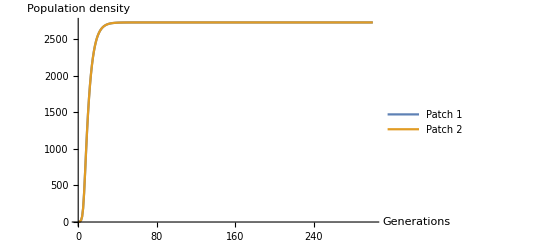

```mathematica
Simulate[x0_,n10_,n20_,a0_,b0_,h0_,s0_,d0_,m0_,α0_,T0_]:=Block[{t=0,n1=n10,n2=n20},
Subscript[Λ, 0]=Λ/.{Subscript[r, 2]->Subscript[r, 2][x,x],Subscript[r, 1]->Subscript[r, 1][x,x]}/.{a->a0,b->b0,h->h0,s->s0,d->d0,m->m0,α->α0}/.x->x0;
Reap[While[t≤T0,
Sow[{t,n1,n2}];
{n1,n2}=Subscript[Λ, 0].{n1,n2}/.Subscript[N, 1]->n1/.Subscript[N, 2]->n2; 
t++;
]
]]
sim=Simulate[0,1,1,400,100,0.5,1,0.2,0.001,0,300]; (* change values here *)
plot1=Map[{#[[1]],#[[2]]}&,sim[[2]][[1]]];
plot2=Map[{#[[1]],#[[3]]}&,sim[[2]][[1]]];
ListLinePlot[{plot1,plot2},PlotRange->All,PlotLegends->{"Patch 1","Patch 2"},AxesLabel->{"Generations","Population density"}]
```

## Invasion fitness

The invasion fitness is the geometric growth rate of an initially rare mutant with trait value y arising in a monomorphic resident population with trait x. It is the leading eigenvalue of the transition matrix of the mutant population dynamics, given by

```mathematica
λ=Λ//Eigenvalues//Last
```

1/2 (r_1-m r_1+r_2-m r_2+√((-r_1+m r_1-r_2+m r_2)^2-4 (r_1 r_2-2 m r_1 r_2)))

The invasion fitness should be one when the mutant phenotype is equal to the resident’s phenotype, when evaluated at deomgraphic equilibrium. That is, at equilibrium the growth rate of the resident should be one. Under some parameter values the demographic equilibrium is

```mathematica
pars={a->400,b->100,h->0.5,s->1,d->0.2,m->0.001,α->0}; (* change values here *)
sol=Solve[{Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]},Subscript[N, 1]>0,Subscript[N, 2]>0}/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x]/.y->x/.x->0/.pars,{Subscript[N, 1],Subscript[N, 2]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N_1→2728.17,N_2→2728.17}}

And the invasion fitness of the resident is

```mathematica
λ/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x]/.y->x/.x->0/.pars/.sol
```

{1.}

At this demographic equilibrium the mutant should be absent, not matter its trait value y. We can check this by solving for the equilibrium mutant dynamics when the resident has reached its steady state:

```mathematica
Solve[Λ .{Subscript[M, 1],Subscript[M, 2]}=={Subscript[M, 1],Subscript[M, 2]}/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x]/.sol/.pars,{Subscript[M, 1],Subscript[M, 2]}][[1]]
```

{M_1→0.,M_2→0.}

We can plot the invasion fitness across trait values of the mutant and of the resident to visualize where evolution through successive trait substitutions will lead. For this, however, we need to compute the ecological equilibrium for each resident trait value. The resulting heatmap is a pairwise invasibility plot.

```mathematica
pars = {a->400,b->100,h->0.75,s->1.6,d->0.2,m->0.001,α->10};(* change values here *)
xvalues=Range[-2,2,0.01];

(* Derive a fitness landscape given a resident value *)
FitnessLandscape=Function[xr, Block[{},

(* Find the ecological equilibrium *)
sol=FindRoot[Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]}/.Subscript[r, 1]-> Subscript[r, 1][x,x]/.Subscript[r, 2]-> Subscript[r, 2][x,x]/.pars/.x->xr,{{Subscript[N, 1],1000},{Subscript[N, 2],1000}}];

(* Parametrize the invasion fitness *)
Subscript[λ, 0]=λ/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x]/.pars/.x->xr/.sol;

(* Test multiple mutant trait values against the resident *)
Map[Sow[{#,xr,Subscript[N, 1]/.sol,Subscript[N, 2]/.sol,Subscript[λ, 0]/.y->#}]&,xvalues];

]];
pip=Quiet[Reap[Map[FitnessLandscape[#]&,xvalues]]]; (* may take some time *)
ListContourPlot[Map[{#[[2]],#[[1]],#[[5]]}&,pip[[2]][[1]]],AxesLabel->{"Resident trait value","Mutant trait value"},Contours->{1}]
```

-Graphics-

```mathematica
Export["pip.csv",pip[[2]][[1]]];
```

## Selection gradient

In the article we derive an expression for the fitness gradient that involves the left and right eigenvectors of the transition matrix, associated with the leading eigenvalue λ. Those eigenvectors are respectively given by

```mathematica
v=(Λ//Transpose//Eigenvectors//Last) m Subscript[r, 2]
u=(Λ//Eigenvectors//Last) m Subscript[r, 1]
```

{1/2 (r_1-m r_1-r_2+m r_2+√(r_1^2-2 m r_1^2+m^2 r_1^2-2 r_1 r_2+4 m r_1 r_2+2 m^2 r_1 r_2+r_2^2-2 m r_2^2+m^2 r_2^2)),m r_2}

{1/2 (r_1-m r_1-r_2+m r_2+√(r_1^2-2 m r_1^2+m^2 r_1^2-2 r_1 r_2+4 m r_1 r_2+2 m^2 r_1 r_2+r_2^2-2 m r_2^2+m^2 r_2^2)),m r_1}

which have the same first element, that is a function of the invasion fitness:

```mathematica
λ-(1-m)Subscript[r, 2]==v[[1]]==u[[1]] //Simplify
v[[1]]=λ-(1-m)Subscript[r, 2];
u[[1]]=λ-(1-m)Subscript[r, 2];
```

True

Let us check that the eigenvectors are valid.

```mathematica
{v.Λ==λ v // Simplify,Λ.u==λ u // Simplify}
```

{True,True}

And let us check that numerically too.

```mathematica
v.Λ/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x]/.pars/.y->1.1/.x->1/.Subscript[N, 1]->100/.Subscript[N, 2]->100
λ v/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x]/.pars/.y->1.1/.x->1/.Subscript[N, 1]->100/.Subscript[N, 2]->100
```

{0.000014955,0.00785442}

{0.000014955,0.00785442}

We find the expression for the selection gradient as per the appendix of the article (evaluated at the resident):

```mathematica
G=v.{{1-m,m}, {m,1-m}}.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.u/(v.u)/.λ->1//Simplify
```

(m^2 dW_2 r_1+dW_1 (1-m-(2-4 m+m^2) r_2+(1-3 m+2 m^2) r_2^2))/(1+(-2+2 m+m^2 r_1) r_2+(-1+m)^2 r_2^2)

where

```mathematica
Subscript[dW, 1][x_]:=D[Subscript[W, 1][y,x],y]/.y->x
Subscript[dW, 2][x_]:=D[Subscript[W, 2][y,x],y]/.y->x
```

This derivation involves some shortcuts in order to get a short explicit expression. We can check its correctness by brute-force differentiating the invasion fitness function. We compare the results to our explicit expression when evaluated with the same parameter values and resident trait (and therefore same ecological equilibrium) as in the previous section:

```mathematica
sol=FindRoot[Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]}/.Subscript[r, 1]-> Subscript[r, 1][x,x]/.Subscript[r, 2]-> Subscript[r, 2][x,x]/.pars/.x->0,{{Subscript[N, 1],1000},{Subscript[N, 2],1000}}]
D[λ/.Subscript[r, 1]-> Subscript[r, 1][y,x]/.Subscript[r, 2]-> Subscript[r, 2][y,x],y]/.y->x/.x->0/.pars/.sol
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{N_1→3051.83,N_2→3051.83}

2.0775×10^-14

```mathematica
G/.Subscript[r, 1]-> Subscript[r, 1][x,x]/.Subscript[r, 2]-> Subscript[r, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x]/.pars/.x->0/.sol
```

-1.23239×10^-12

Evolutionary equilibria  are values of x at which the selection gradient is zero. Because the selection gradient depends on equilibrium population densities, which depend on x, we solve the ecological and the evolutionary dynamics together to find trait values which cancel the gradient when evaluated at ecological equilibrium.

```mathematica
sol=FindRoot[{Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]},G==0}/.Subscript[r, 1]->Subscript[r, 1][z,z]/.Subscript[r, 2]->Subscript[r, 2][z,z]/.Subscript[dW, 1]-> Subscript[dW, 1][z]/.Subscript[dW, 2]->Subscript[dW, 2][z]/.pars,{{Subscript[N, 1],1000},{Subscript[N, 2],1000},{z,0.1}},MaxIterations->1000]
```

{N_1→2728.17,N_2→2728.17,z→-2.3463×10^-11}

## Fitness curvature

We derived the curvature of the fitness function using similar shortcuts as for the selection gradient (see appendix):

```mathematica
dv={(m-1)Subscript[dW, 2],m Subscript[dW, 2]};
du={(m-1)Subscript[dW, 2],m Subscript[dW, 1]};
M={{1-m,m},{m,1-m}};
ddλ=(dv.M.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.u + v.M.{{Subscript[ddW, 1]-α Subscript[W, 1],0},{0,Subscript[ddW, 2]-α Subscript[W, 2]}}.u + v.M.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.du)/(v.u)/.λ->1//FullSimplify
```

(m^2 ddW_2 r_1+2 (-1+2 m) dW_1 dW_2 (1+(-1+m) r_2)+ddW_1 (1+(-1+m) r_2) (1-m+(-1+2 m) r_2)-α W_1+m α W_1+2 α r_2 W_1-4 m α r_2 W_1+m^2 α r_2 W_1-α r_2^2 W_1+3 m α r_2^2 W_1-2 m^2 α r_2^2 W_1-m^2 α r_1 W_2)/(1+r_2 (m^2 r_1+(-1+m) (2+(-1+m) r_2)))

where

```mathematica
Subscript[ddW, 1][x_]:=D[D[Subscript[W, 1][y,x],y],y]/.y->x
Subscript[ddW, 2][x_]:=D[D[Subscript[W, 2][y,x],y],y]/.y->x
```

Again, we can check the correctness of this derivation by comparing its result to brute-force differentiation of the invasion fitness for given parameter values.

```mathematica
ddλ/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x]/.Subscript[ddW, 1]->Subscript[ddW, 1][x]/.Subscript[ddW, 2]->Subscript[ddW, 2][x]/.Subscript[W, 1]->Subscript[W, 1][x,x]/.Subscript[W, 2]->Subscript[W, 2][x,x]/.x->z/.pars/.sol
```

18.1422

```mathematica
D[D[λ/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x],y],y]/.y->x/.x->z/.pars/.sol
```

18.1422

## Attainability

```mathematica
D[G/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x]/.Subscript[N, 1]->Subscript[N, 1][x]/.Subscript[N, 2]->Subscript[N, 2][x],x];
```

```mathematica
Subscript[N, 1][x0_]:=Subscript[N, 1]/.FindRoot[Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]}/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.pars/.x->x0,{{Subscript[N, 1],1000},{Subscript[N, 2],1000}}];
Subscript[N, 2][x0_]:=Subscript[N, 2]/.FindRoot[Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]}/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.pars/.x->x0,{{Subscript[N, 1],1000},{Subscript[N, 2],1000}}];
{D[Subscript[N, 1][x],x]/.x->0,Subscript[N, 2][0]}
```

{∂_0 2728.17,2728.17}

```mathematica
Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]}/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.pars
```

{0.999 N_1 (0.8+(200. ⅇ^(-(-1+x)^2))/(100+ⅇ^(-(-1+x)^2) N_1)+(400 ⅇ^(-(1+x)^2))/(100+ⅇ^(-(1+x)^2) N_1))+0.001 N_2 (0.8+(400 ⅇ^(-(-1+x)^2))/(100+ⅇ^(-(-1+x)^2) N_2)+(200. ⅇ^(-(1+x)^2))/(100+ⅇ^(-(1+x)^2) N_2)),0.001 N_1 (0.8+(200. ⅇ^(-(-1+x)^2))/(100+ⅇ^(-(-1+x)^2) N_1)+(400 ⅇ^(-(1+x)^2))/(100+ⅇ^(-(1+x)^2) N_1))+0.999 N_2 (0.8+(400 ⅇ^(-(-1+x)^2))/(100+ⅇ^(-(-1+x)^2) N_2)+(200. ⅇ^(-(1+x)^2))/(100+ⅇ^(-(1+x)^2) N_2))}=={N_1,N_2}

```mathematica
Solve[Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]}/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.pars,{Subscript[N, 1],Subscript[N, 2]}]
```

$Aborted

This section has problems. The attainability of the equilibrium z is determined by the change in direction of the selection gradient as the resident trait value increases through the equilibrium value. In the appendix and using the same shortcuts as before we derive the following expression

```mathematica
dxv={(m-1)Subscript[dxW, 2],m Subscript[dxW, 2]};
dxu={(m-1)Subscript[dxW, 2],m Subscript[dxW, 1]};
dG=(dxv.M.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.u+v.M.{{Subscript[ddxW, 1],0},{0,Subscript[ddxW, 2]}}.u+v.M.{{Subscript[dW, 1],0},{0,Subscript[dW, 2]}}.dxu)/(v.u)/.λ->1//FullSimplify
```

(-2 dW_1 dxW_2+m (m dW_2 dxW_1-(-4+m) dW_1 dxW_2+m ddxW_2 r_1)+2 (-1+m) (-1+2 m) dW_1 dxW_2 r_2+ddxW_1 (1+(-1+m) r_2) (1-m+(-1+2 m) r_2))/(1+r_2 (m^2 r_1+(-1+m) (2+(-1+m) r_2)))

where

```mathematica
Subscript[dxW, 1][x_]:=D[Subscript[W, 1][x,x],x];
Subscript[dxW, 2][x_]:=D[Subscript[W, 2][x,x],x];
Subscript[ddxW, 1][x_]:=D[D[Subscript[W, 1][y,x],y]/.y->x,x];
Subscript[ddxW, 2][x_]:=D[D[Subscript[W, 2][y,x],y]/.y->x,x];
```

Evaluating this expression under some parameters and at a given equilibrium we get

```mathematica
dG/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x]/.Subscript[dxW, 1]->Subscript[dxW, 1][x]/.Subscript[dxW, 2]->Subscript[dxW, 2][x]/.Subscript[ddxW, 1]->Subscript[ddxW, 1][x]/.Subscript[ddxW, 2]->Subscript[ddxW, 2][x]/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.x->z/.pars/.sol
```

1.2801

which we can compare to directly differentiating the selection gradient,

```mathematica
D[G/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x],x]/.x->z/.pars/.sol
```

1.2801

or even differentiating the fitness function

```mathematica
D[D[λ/.Subscript[r, 1]->Subscript[r, 1][y,x]/.Subscript[r, 2]->Subscript[r, 2][y,x],y]/.y->x,x]/.x->z/.pars/.sol
```

1.2801

How come the convergence stability criterion is positive in this example? This means that the evolutionary equilibrium is not attainable, while we clearly see in the pairwise invasibility plot above that the equilibrium x=0 is a branching point, i.e. it is convergence stable and evolutionarily unstable. What is going on here?

Let us compare the pairwise invasibility plot to the convergence stability criterion computed across values of the resident trait value.

```mathematica
p1=ListContourPlot[Map[{#[[2]],#[[1]],#[[5]]}&,pip[[2]][[1]]],AxesLabel->{"Resident trait value","Mutant trait value"},Contours->{1}];
```

```mathematica
ComputeConvergence[x0_]:=Block[{},
(* Find equilibrium resident densities *)
sol=FindRoot[Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]}/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.pars/.x->x0,{{Subscript[N, 1],1000},{Subscript[N, 2],1000}}];
(* Compute convergence stability *)
grad=G/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x]/.pars/.sol/.x->x0;
dgrad=D[G/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x],x]/.pars/.sol/.x->x0;
Sow[{x0,grad,dgrad}];
]
gradient=Map[#[[1;;2]]&,Quiet[Reap[Map[ComputeConvergence[#]&,Range[-0.0000001,0.0000001,0.000000001]]][[2]][[1]]]];
convergence=Map[{#[[1]],#[[3]]}&,Quiet[Reap[Map[ComputeConvergence[#]&,Range[-0.0000001,0.0000001,0.000000001]]][[2]][[1]]]];
```

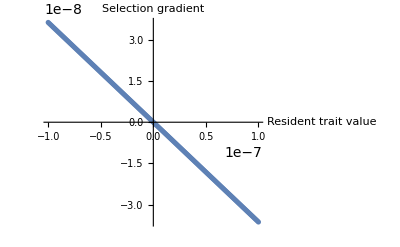

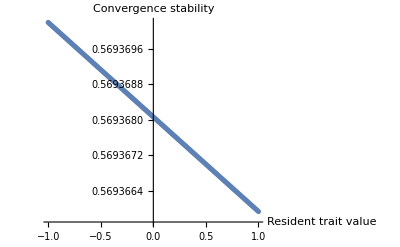

```mathematica
p2=ListPlot[gradient,AxesLabel->{"Resident trait value", "Selection gradient"}]
p3=ListPlot[convergence,AxesLabel->{"Resident trait value", "Convergence stability"}]
```

If we show both plots side by side (you may have to magnify the right one manually), we see that the trait value 0 should be a branching point, but the convergence stability criterion is positive at x = 0, meaning that this equilibrium is not attainable.... I do not know why this is.

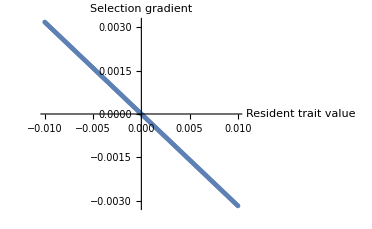
{-Graphics-,-Graphics-}

```mathematica
{p1,p2}
```

For now we will use the difference in selection gradient to evaluate convergence stability.

## Numerical procedures

We used the following script to explore singularities and their stability across parameter space. First we define fixed and variable parameters. We establish all parameter combinations we are going to test. For each parameter combination, there may be multiple equilibria, therefore we repeat the numerical search of the roots of the selection gradient with various starting points between x_min and x_max. For each combination of equilibrium trait value and population densities, we evaluate the curvature of the fitness function and the change in direction of the selection gradient.

```mathematica
(* Parametrization *)
fixed={a->400,b->100,d->0.2};
nstart=1000;
step=0.00001;
hvalues=Range[0,1,0.01];
svalues=Range[0,2,0.01]; svalues[[1]]=0.01;
αvalues={0,1,10};
mvalues={0.001,0.01};
xvalues=Range[-1,0,0.1]; (* between xmin and xmax *)
parvalues = Tuples[{hvalues,svalues,αvalues,mvalues,xvalues}];
listpars=Map[{h->#[[1]],s->#[[2]],α->#[[3]],m->#[[4]],x->#[[5]]}&,parvalues];

(* Initialize expressions *)
dynamics={Λ.{Subscript[N, 1],Subscript[N, 2]}=={Subscript[N, 1],Subscript[N, 2]},G==0}/.Subscript[r, 1]->Subscript[r, 1][z,z]/.Subscript[r, 2]->Subscript[r, 2][z,z]/.Subscript[dW, 1]-> Subscript[dW, 1][z]/.Subscript[dW, 2]->Subscript[dW, 2][z]/.fixed;
Subscript[ddλ, 0]=ddλ/.Subscript[r, 1]-> Subscript[r, 1][z,z]/.Subscript[r, 2]-> Subscript[r, 2][z,z]/.Subscript[W, 1]->Subscript[W, 1][z,z]/.Subscript[W, 2]->Subscript[W, 2][z,z]/.Subscript[dW, 1]-> Subscript[dW, 1][z]/.Subscript[dW, 2]->Subscript[dW, 2][z]/.Subscript[ddW, 1]->Subscript[ddW, 1][z]/.Subscript[ddW, 2]->Subscript[ddW, 2][z]/.fixed;
(* dG=dG/.Subscript[r, 1]->Subscript[r, 1][z,z]/.Subscript[r, 2]->Subscript[r, 2][z,z]/.Subscript[dWx, 1]->Subscript[dWx, 1][z]/.Subscript[dWx, 2]->Subscript[dWx, 2][z]/.fixed; *)
Subscript[G, 0]=G/.Subscript[r, 1]->Subscript[r, 1][x,x]/.Subscript[r, 2]->Subscript[r, 2][x,x]/.Subscript[dW, 1]->Subscript[dW, 1][x]/.Subscript[dW, 2]->Subscript[dW, 2][x]/.fixed;

(* Core analytical module *)
AnalyzeDynamics=Compile[{pars}, Block[{},
sol=FindRoot[dynamics/.pars,{{Subscript[N, 1],nstart},{Subscript[N, 2],nstart},{z,x/.pars}}];
inv=Subscript[ddλ, 0]/.pars/.sol;
zvalue=z/.sol;
solbefore=FindRoot[dynamics[[1]]/.pars/.z-> zvalue-step,{{Subscript[N, 1],1000},{Subscript[N, 2],1000}}];
gradbefore=Subscript[G, 0]/.pars/.solbefore/.x->z-step/.sol;
solafter=FindRoot[dynamics[[1]]/.pars/.z-> zvalue+step,{{Subscript[N, 1],1000},{Subscript[N, 2],1000}}];
gradafter=Subscript[G, 0]/.pars/.solafter/.x->z+step/.sol;
conv=gradafter-gradbefore;
Sow[{sol,inv,conv}];
],CompilationTarget->"C"];

(* Loop through parameter combinations *)
ExploreDynamics=Compile[{listpars}, Block[{},Reap[Map[AnalyzeDynamics[#]&,listpars]]],CompilationTarget->"C",Parallelization->True];

results=Quiet[ExploreDynamics[listpars][[2]]]; (* this may take a while *)
```

FindRoot::nlnum: The function value {-1000.+Λ.{1000.,1000.},-1000.+Λ.{1000.,1000.},G} is not a list of numbers with dimensions {3} at {N_1,N_2,z} = {1000.,1000.,-1.}.

ReplaceAll::reps: {FindRoot[dynamics/.{h→0.,s→0.01,α→0,m→0.001,x→-1.},{{N_1,nstart},{N_2,nstart},{z,x/.{h→0.,s→0.01,α→0,m→0.001,x→-1.}}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-1000.+Λ.{1000.,1000.},-1000.+Λ.{1000.,1000.},G} is not a list of numbers with dimensions {3} at {N_1,N_2,z} = {1000.,1000.,0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[dynamics/.{h→1.,s→2.,α→10,m→0.01,x→0.},{{N_1,nstart},{N_2,nstart},{z,x/.{h→1.,s→2.,α→10,m→0.01,x→0.}}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(* Assemble a dataset with the results and the parameter values *)
equilibria=Map[{Subscript[N, 1],Subscript[N, 2],z}/.#[[1]]&,results[[1]]];
stability=Map[#[[2;;3]]&,results[[1]]];
dataset=MapThread[Flatten[{#1,#2,#3}]&,{parvalues,equilibria,stability}];

(* Structure of the dataset *)
(* Column 1: value of h *)
(* Column 2: value of s *)
(* Column 3: value of alpha *)
(* Column 4: value of m *)
(* Column 5: starting search value for x *)
(* Column 6: Equilibrium value of N1 *)
(* Column 7: Equilibrium value of N2 *)
(* Column 8: Equilibrium value of x *)
(* Column 9: Evolutionary invasibility of the equilibrium *)
(* Column 10: Evolutionary attainability of the equilibrium *)
```

Part::partd: Part specification results⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {results⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression {N_1,N_2,z}/.1⟦1⟧ cannot be used as a part specification.

Part::partd: Part specification results⟦1⟧ is longer than depth of object.

Part::take: Cannot take positions 2 through 3 in results.

Part::take: Cannot take positions 2 through 3 in 1.

Part::pkspec1: The expression 1⟦2;;3⟧ cannot be used as a part specification.

MapThread::mptd: Object parvalues at position {2, 1} in MapThread[Flatten[{#1,#2,#3}]&,{parvalues,({N_1,N_2,z}/.results⟦1⟧)⟦{N_1,N_2,z}/.1⟦1⟧⟧,results⟦2;;3⟧⟦1⟦2;;3⟧⟧}] has only 0 of required 1 dimensions.

```mathematica
dataset
```

{{0.,0.01,0,0.001,-1.,1898.99,1898.99,-1.37339×10^-11,0.012048,-1.13874×10^-6},609028,{1.,2.,6,-2.70462,-1.19537×10^-8}}
 |  |  |  |

```mathematica
(* Save the output to file *)
Export["adaptive_dynamics2.csv",dataset];
```